```mathematica
Clear[kd];
Clear[ku];
Clear[md];
Clear[mu];
Clear[ξ];
Clear[x];
Clear[i];
Clear[t];

Simplify[Series[EbarTDDu1[i,x,ξ,t],{ξ,0,2}]]
Simplify[Series[EbarTDDd1[i,x,ξ,t],{ξ,0,2}]]
Simplify[Series[HTDDu1[i,x,ξ,t],{ξ,0,2}]]
Simplify[Series[HTDDd1[i,x,ξ,t],{ξ,0,2}]]
EbarTDDuser[i_,x_,ξ_,t_]:=-1. (x^(-2+mu[t,i]) (-1.+1. x)^3)-(1.5 (x^(-2+mu[t,i]) mu[t,i] (-5.551115123125783*^-17+1.6653345369377348*^-16 x^2-2.7755575615628914*^-17 mu[t,i]^2)) ξ)/(-1.+mu[t,i]^2)+1/(-1.+mu[t,i]^2)x^(-4+mu[t,i]) (-0.6000000000000001+1. x-0.9999999999999999 x^4+0.6000000000000001 x^5+(0.5000000000000001-1.5000000000000009 x+1.0000000000000018 x^2+0.9999999999999979 x^3-1.4999999999999993 x^4+0.49999999999999967 x^5) mu[t,i]+(0.5-0.49999999999999994 x-0.9999999999999997 x^2+1. x^3+0.5000000000000001 x^4-0.4999999999999998 x^5) mu[t,i]^2+(-0.5000000000000001+1.5 x-0.9999999999999999 x^2-1.0000000000000002 x^3+1.5 x^4-0.5000000000000001 x^5) mu[t,i]^3+(0.1-0.5 x+0.9999999999999999 x^2-1. x^3+0.49999999999999994 x^4-0.1 x^5) mu[t,i]^4) ξ^2;

EbarTDDdser[i_,x_,ξ_,t_]:=-1. (x^(-2+md[t,i]) (-1.+1. x)^3)-(1.5 (x^(-2+md[t,i]) md[t,i] (-5.551115123125783*^-17+1.6653345369377348*^-16 x^2-2.7755575615628914*^-17 md[t,i]^2)) ξ)/(-1.+md[t,i]^2)+1/(-1.+md[t,i]^2)x^(-4+md[t,i]) (-0.6000000000000001+1. x-0.9999999999999999 x^4+0.6000000000000001 x^5+(0.5000000000000001-1.5000000000000009 x+1.0000000000000018 x^2+0.9999999999999979 x^3-1.4999999999999993 x^4+0.49999999999999967 x^5) md[t,i]+(0.5-0.49999999999999994 x-0.9999999999999997 x^2+1. x^3+0.5000000000000001 x^4-0.4999999999999998 x^5) md[t,i]^2+(-0.5000000000000001+1.5 x-0.9999999999999999 x^2-1.0000000000000002 x^3+1.5 x^4-0.5000000000000001 x^5) md[t,i]^3+(0.1-0.5 x+0.9999999999999999 x^2-1. x^3+0.49999999999999994 x^4-0.1 x^5) md[t,i]^4) ξ^2;

HTDDuser[i_,x_,ξ_,t_]:=-1. (x^(-2+ku[t,i]) (-1.+1. x)^3)-(1.5 (x^(-2+ku[t,i]) ku[t,i] (-5.551115123125783*^-17+1.6653345369377348*^-16 x^2-2.7755575615628914*^-17 ku[t,i]^2)) ξ)/(-1.+ku[t,i]^2)+1/(-1.+ku[t,i]^2)x^(-4+ku[t,i]) (-0.6000000000000001+1. x-0.9999999999999999 x^4+0.6000000000000001 x^5+(0.5000000000000001-1.5000000000000009 x+1.0000000000000018 x^2+0.9999999999999979 x^3-1.4999999999999993 x^4+0.49999999999999967 x^5) ku[t,i]+(0.5-0.49999999999999994 x-0.9999999999999997 x^2+1. x^3+0.5000000000000001 x^4-0.4999999999999998 x^5) ku[t,i]^2+(-0.5000000000000001+1.5 x-0.9999999999999999 x^2-1.0000000000000002 x^3+1.5 x^4-0.5000000000000001 x^5) ku[t,i]^3+(0.1-0.5 x+0.9999999999999999 x^2-1. x^3+0.49999999999999994 x^4-0.1 x^5) ku[t,i]^4) ξ^2;
HTDDdser[i_,x_,ξ_,t_]:=-1. (x^(-2+kd[t,i]) (-1.+1. x)^3)-(1.5 (x^(-2+kd[t,i]) kd[t,i] (-5.551115123125783*^-17+1.6653345369377348*^-16 x^2-2.7755575615628914*^-17 kd[t,i]^2)) ξ)/(-1.+kd[t,i]^2)+1/(-1.+kd[t,i]^2)x^(-4+kd[t,i]) (-0.6000000000000001+1. x-0.9999999999999999 x^4+0.6000000000000001 x^5+(0.5000000000000001-1.5000000000000009 x+1.0000000000000018 x^2+0.9999999999999979 x^3-1.4999999999999993 x^4+0.49999999999999967 x^5) kd[t,i]+(0.5-0.49999999999999994 x-0.9999999999999997 x^2+1. x^3+0.5000000000000001 x^4-0.4999999999999998 x^5) kd[t,i]^2+(-0.5000000000000001+1.5 x-0.9999999999999999 x^2-1.0000000000000002 x^3+1.5 x^4-0.5000000000000001 x^5) kd[t,i]^3+(0.1-0.5 x+0.9999999999999999 x^2-1. x^3+0.49999999999999994 x^4-0.1 x^5) kd[t,i]^4) ξ^2;
```

Piecewise[{{0., (ξ∈ℝ&&x<0)||(x==0&&ξ<0)}, {-1. (x^(-2+mu[t,i]) (-1.+1. x)^3)-(1.5 (x^(-2+mu[t,i]) mu[t,i] (-5.55112×10^-17+1.66533×10^-16 x^2-2.77556×10^-17 mu[t,i]^2)) ξ)/(-1.+mu[t,i]^2)+(x^(-4+mu[t,i]) (-0.6+1. x-1. x^4+0.6 x^5+(0.5-1.5 x+1. x^2+1. x^3-1.5 x^4+0.5 x^5) mu[t,i]+(0.5-0.5 x-1. x^2+1. x^3+0.5 x^4-0.5 x^5) mu[t,i]^2+(-0.5+1.5 x-1. x^2-1. x^3+1.5 x^4-0.5 x^5) mu[t,i]^3+(0.1-0.5 x+1. x^2-1. x^3+0.5 x^4-0.1 x^5) mu[t,i]^4) ξ^2)/(-1.+mu[t,i]^2)+O[ξ]^3, ξ∈ℝ&&x>0}, {ξ^mu[t,i] (1.5/((-1.+mu[t,i]^2) ξ^2)-1.5/(mu[t,i] ξ)+(-1.5+0.75 mu[t,i]+0.75 mu[t,i]^2)/(-1.+mu[t,i]^2)+((0.75+0.25 mu[t,i]-0.75 mu[t,i]^2-0.25 mu[t,i]^3) ξ)/(-1.+mu[t,i]^2)+((-0.5-0.375 mu[t,i]+0.4375 mu[t,i]^2+0.375 mu[t,i]^3+0.0625 mu[t,i]^4) ξ^2)/(-1.+mu[t,i]^2)+O[ξ]^3), True}}]

Piecewise[{{0., (ξ∈ℝ&&x<0)||(x==0&&ξ<0)}, {-1. (x^(-2+md[t,i]) (-1.+1. x)^3)-(1.5 (x^(-2+md[t,i]) md[t,i] (-5.55112×10^-17+1.66533×10^-16 x^2-2.77556×10^-17 md[t,i]^2)) ξ)/(-1.+md[t,i]^2)+(x^(-4+md[t,i]) (-0.6+1. x-1. x^4+0.6 x^5+(0.5-1.5 x+1. x^2+1. x^3-1.5 x^4+0.5 x^5) md[t,i]+(0.5-0.5 x-1. x^2+1. x^3+0.5 x^4-0.5 x^5) md[t,i]^2+(-0.5+1.5 x-1. x^2-1. x^3+1.5 x^4-0.5 x^5) md[t,i]^3+(0.1-0.5 x+1. x^2-1. x^3+0.5 x^4-0.1 x^5) md[t,i]^4) ξ^2)/(-1.+md[t,i]^2)+O[ξ]^3, ξ∈ℝ&&x>0}, {ξ^md[t,i] (1.5/((-1.+md[t,i]^2) ξ^2)-1.5/(md[t,i] ξ)+(-1.5+0.75 md[t,i]+0.75 md[t,i]^2)/(-1.+md[t,i]^2)+((0.75+0.25 md[t,i]-0.75 md[t,i]^2-0.25 md[t,i]^3) ξ)/(-1.+md[t,i]^2)+((-0.5-0.375 md[t,i]+0.4375 md[t,i]^2+0.375 md[t,i]^3+0.0625 md[t,i]^4) ξ^2)/(-1.+md[t,i]^2)+O[ξ]^3), True}}]

Piecewise[{{0., (ξ∈ℝ&&x<0)||(x==0&&ξ<0)}, {-1. (x^(-2+ku[t,i]) (-1.+1. x)^3)-(1.5 (x^(-2+ku[t,i]) ku[t,i] (-5.55112×10^-17+1.66533×10^-16 x^2-2.77556×10^-17 ku[t,i]^2)) ξ)/(-1.+ku[t,i]^2)+(x^(-4+ku[t,i]) (-0.6+1. x-1. x^4+0.6 x^5+(0.5-1.5 x+1. x^2+1. x^3-1.5 x^4+0.5 x^5) ku[t,i]+(0.5-0.5 x-1. x^2+1. x^3+0.5 x^4-0.5 x^5) ku[t,i]^2+(-0.5+1.5 x-1. x^2-1. x^3+1.5 x^4-0.5 x^5) ku[t,i]^3+(0.1-0.5 x+1. x^2-1. x^3+0.5 x^4-0.1 x^5) ku[t,i]^4) ξ^2)/(-1.+ku[t,i]^2)+O[ξ]^3, ξ∈ℝ&&x>0}, {ξ^ku[t,i] (1.5/((-1.+ku[t,i]^2) ξ^2)-1.5/(ku[t,i] ξ)+(-1.5+0.75 ku[t,i]+0.75 ku[t,i]^2)/(-1.+ku[t,i]^2)+((0.75+0.25 ku[t,i]-0.75 ku[t,i]^2-0.25 ku[t,i]^3) ξ)/(-1.+ku[t,i]^2)+((-0.5-0.375 ku[t,i]+0.4375 ku[t,i]^2+0.375 ku[t,i]^3+0.0625 ku[t,i]^4) ξ^2)/(-1.+ku[t,i]^2)+O[ξ]^3), True}}]

Piecewise[{{0., (ξ∈ℝ&&x<0)||(x==0&&ξ<0)}, {-1. (x^(-2+kd[t,i]) (-1.+1. x)^3)-(1.5 (x^(-2+kd[t,i]) kd[t,i] (-5.55112×10^-17+1.66533×10^-16 x^2-2.77556×10^-17 kd[t,i]^2)) ξ)/(-1.+kd[t,i]^2)+(x^(-4+kd[t,i]) (-0.6+1. x-1. x^4+0.6 x^5+(0.5-1.5 x+1. x^2+1. x^3-1.5 x^4+0.5 x^5) kd[t,i]+(0.5-0.5 x-1. x^2+1. x^3+0.5 x^4-0.5 x^5) kd[t,i]^2+(-0.5+1.5 x-1. x^2-1. x^3+1.5 x^4-0.5 x^5) kd[t,i]^3+(0.1-0.5 x+1. x^2-1. x^3+0.5 x^4-0.1 x^5) kd[t,i]^4) ξ^2)/(-1.+kd[t,i]^2)+O[ξ]^3, ξ∈ℝ&&x>0}, {ξ^kd[t,i] ((1.5 ku[t,i])/(kd[t,i] (-1.+kd[t,i]^2) ξ^2)+(1.5-1.5 kd[t,i] ku[t,i])/(kd[t,i] (-1.+kd[t,i]^2) ξ)+(-1.5+(0.75+0.75 kd[t,i]) ku[t,i])/(-1.+kd[t,i]^2)+((0.75+kd[t,i] (0.75-0.75 ku[t,i])-0.5 ku[t,i]-0.25 kd[t,i]^2 ku[t,i]) ξ)/(-1.+kd[t,i]^2)+((-0.5+kd[t,i]^2 (-0.25+0.375 ku[t,i])+kd[t,i] (-0.75+0.6875 ku[t,i])+0.375 ku[t,i]+0.0625 kd[t,i]^3 ku[t,i]) ξ^2)/(-1.+kd[t,i]^2)+O[ξ]^3), True}}]

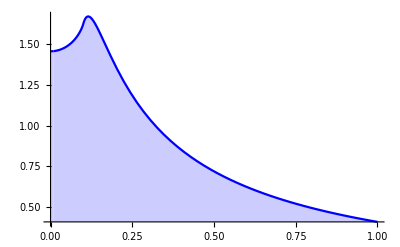

-Graphics-

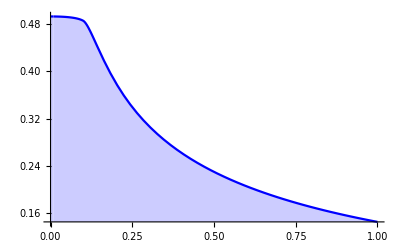

-Graphics-

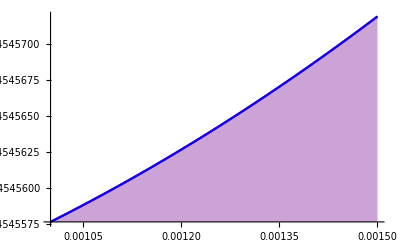

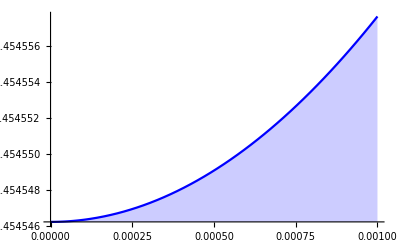

-Graphics-

-Graphics-

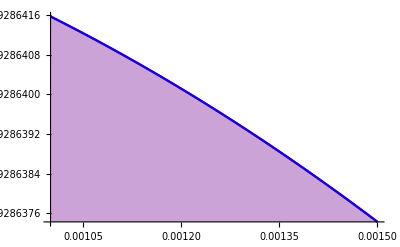

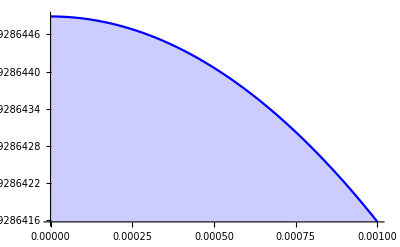

-Graphics-

-Graphics-

```mathematica
ii=0; xx=0.1; tt=-0.0; ξmin=0.0; ξmax=1.0;
Plot[{EbarTDDu[ii,xx,ξ,tt]},{ξ,ξmin, ξmax},PlotRange->All,PlotStyle->{Red,Blue},Filling->Axis]
Plot[{EbarTDDd[ii,xx,ξ,tt]},{ξ,ξmin, ξmax},PlotRange->All,PlotStyle->{Red,Blue},Filling->Axis]
Plot[{HTDDu[ii,xx,ξ,tt]},{ξ,ξmin, ξmax},PlotRange->All,PlotStyle->{Red,Blue},Filling->Axis]
Plot[{HTDDd[ii,xx,ξ,tt]},{ξ,ξmin, ξmax},PlotRange->All,PlotStyle->{Red,Blue},Filling->Axis]

Plot[{EbarTDDu1[ii,xx,ξ,tt],EbarTDDuser[ii,xx,ξ,tt]},{ξ,0.001,0.0015},PlotRange->All,PlotStyle->{Red,Blue},Filling->Axis]
Plot[{EbarTDDuser[ii,xx,ξ,tt]},{ξ,0.00,0.001},PlotRange->All,PlotStyle->{Red,Blue},Filling->Axis]
Plot[{EbarTDDd1[ii,xx,ξ,tt],EbarTDDdser[ii,xx,ξ,tt]},{ξ,0.001,0.0015},PlotRange->All,PlotStyle->{Red,Blue},Filling->Axis]
Plot[{EbarTDDdser[ii,xx,ξ,tt]},{ξ,0.00,0.001},PlotRange->All,PlotStyle->{Red,Blue},Filling->Axis]
Plot[{HTDDu1[ii,xx,ξ,tt],HTDDuser[ii,xx,ξ,tt]},{ξ,0.001,0.0015},PlotRange->All,PlotStyle->{Red,Blue},Filling->Axis]
Plot[{HTDDuser[ii,xx,ξ,tt]},{ξ,0.00,0.001},PlotRange->All,PlotStyle->{Red,Blue},Filling->Axis]
Plot[{HTDDd1[ii,xx,ξ,tt],HTDDdser[ii,xx,ξ,tt]},{ξ,0.001,0.0015},PlotRange->All,PlotStyle->{Red,Blue},Filling->Axis]
Plot[{HTDDdser[ii,xx,ξ,tt]},{ξ,0.00,0.001},PlotRange->All,PlotStyle->{Red,Blue},Filling->Axis]
```

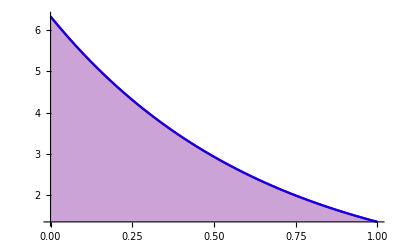

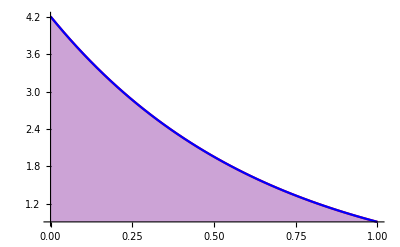

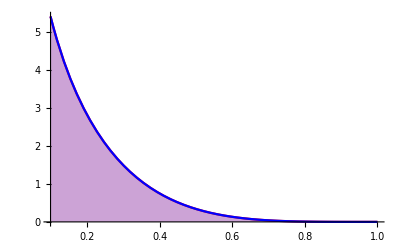

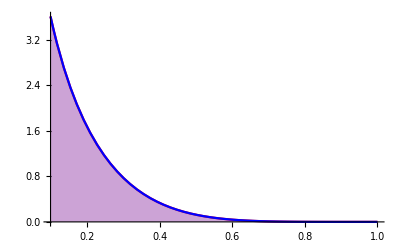

General::ivar: 0.00100001 is not a valid variable.

```mathematica
Au=0.0;
Bu=0.5;
αu=0.3;
αu'=0.45;
nu=4.83;
βu=4;
ETPFu[x_]:=(Bu+αu'Log[1./x]);
ETFLu[x_]:=nu*x^-αu*(1.-x)^βu;


Ad=0.0;
Bd=0.5;
αd=0.3;
αd'=0.45;
nd=3.57;
βd=5;
ETPFd[x_]:=(Bd+αd'Log[1./x]);
ETFLd[x_]:=nd*x^-αd*(1.-x)^βd;

ETu[x_,t_]:=ETFLu[x]*Exp[ETPFu[x]*t];
ETd[x_,t_]:=ETFLd[x]*Exp[ETPFd[x]*t];
xx=0.1; tt=-0.1;
Plot[{ETu[xx,-t],EbarTu[xx,0.,-t]},{t,0,1},PlotRange->All,PlotStyle->{Red,Blue},Filling->Axis]
Plot[{ETd[xx,-t],EbarTd[xx,0.,-t]},{t,0,1},PlotRange->All,PlotStyle->{Red,Blue},Filling->Axis]

Plot[{ETu[x,tt],EbarTu[x,0.,tt]},{x,0.1,1},PlotRange->All,PlotStyle->{Red,Blue},Filling->Axis]
Plot[{ETd[x,tt],EbarTd[x,0.,tt]},{x,0.1,1},PlotRange->All,PlotStyle->{Red,Blue},Filling->Axis]
```